```mathematica
(*Vector modification of RK45,so use error vector and its norm for step changes*)
(*Find the solution as long as cond evaluates to True*)
RK45Rocket[f_,t0_,h0_,tol_,y0_,cond_]:=Module[{
a=N@{0,1/4,3/8,12/13,1,1/2},
(*b=N@{
{0,1/4,3/32,1932/2197,439/216,-8/27},
{0,0,9/32,-7200/2197,-8,2},
{0,0,0,7296/2197,3680/513,-3544/2565},
{0,0,0,0,-845/4104,1859/4104},
{0,0,0,0,0,-11/40},
{0,0,0,0,0,0}
},*)
b=N@{
{0,0,0,0,0,0},
{1/4,0,0,0,0,0},
{3/32,9/32,0,0,0,0},
{1932/2197,-7200/2197,7296/2197,0,0,0},
{439/216,-8,3680/513,-845/4104,0,0},
{-8/27,2,-3544/2565,1859/4104,-11/40,0}
},
p=N@{
{16/135,0,6656/12825,28561/56430,-9/50,2/55},
{25/216,0,1408/2565,2197/4104,-1/5,0}
},
y={y0},t={t0},err={0},
tc=t0,yc=y0,hc=h0,
k,s,errcvec,errc,hnext
},

While[cond@yc,
k=ConstantArray[0,{4,6}];
For[s=1,s≤6,s++,
k⟦All,s⟧=hc*f[tc+a⟦s⟧hc,yc+k.b⟦s⟧];
];

errcvec=k.(p⟦1⟧-p⟦2⟧);
errc=(Norm@errcvec)/(Norm@yc);
hnext=hc*(tol/errc)^(1/5);
If[errc>tol,hc=hnext;Continue[]];

yc+=k.p⟦1⟧;
AppendTo[y,yc];
tc+=hc;
AppendTo[t,tc];
AppendTo[err,errc];
hc=hnext;
];

{t,y,err}
]
```

```mathematica
(* Example problem *)
c=0.2;
g=9.81;
m=15;
rho=1.29;
s=0.25;

t0=0;
x0=0;
y0=0;
v0=50;
theta0=0.6;

f[t_,u_List]:={u⟦3⟧ Cos[u⟦4⟧],u⟦3⟧Sin[u⟦4⟧],-(c rho s u⟦3⟧^2)/(2*m)-g Sin[u⟦4⟧],-(g*Cos[u⟦4⟧])/u⟦3⟧};

u0={x0,y0,v0,theta0};
h0=0.01;
tol=10^(-7);
```

```mathematica
(* Solution *)
cond=#⟦2⟧≥0&;
rcktTrj=RK45Rocket[f,t0,h0,tol,u0,cond];
m=Length[rcktTrj⟦1⟧];
coords=rcktTrj⟦2⟧;
interpolation=Interpolation[#⟦{1,2}⟧&/@coords, Method->"Spline"];
approxFall=x/.FindRoot[interpolation@x==0,{x,coords⟦-1,1⟧}];
```

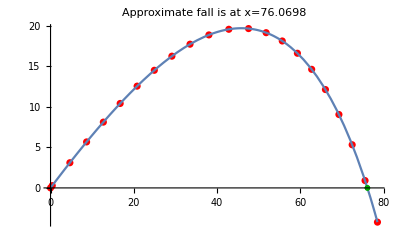

```mathematica
(* Plotting *)
pointPlot=ListPlot[Table[{coords⟦k,1⟧,coords⟦k,2⟧},{k,1,m}],PlotStyle->Red,PlotLabel->Style["Approximate fall is at x="<>ToString[approxFall],FontSize->16]];
interPlot=Plot[interpolation@x,{x,x0,coords⟦-1,1⟧}];
fallPlot=ListPlot[{{approxFall,0}},PlotStyle->Darker@Green,PlotMarkers->"OpenMarkers"];
Show[pointPlot,interPlot,fallPlot]
```